Evidence of H_1, P(D|H_1)

```mathematica
t=w0+w1 x;
```

```mathematica
w1=0;1/(2π)Exp[(-(y)^2)/2] 1/(2π)/.y->{8,10,11}//N
```

{3.20787×10^-16,4.88558×10^-24,1.34532×10^-28}

```mathematica
L1={4.062500444221496*^-30,9.423062528246402*^-46,7.145094103642068*^-55};
```

```mathematica
evidence1=Product[L1[[i]],{i,1,3}]
```

2.73523×10^-129

Evidence of H_2, P(D|H_2)

```mathematica
Clear[w1,y]
```

```mathematica
1/(2π)Exp[-w1^2] 1/(2π)Exp[-(t-y)^2] 1/(2π)
```

(ⅇ^(-w1^2-(w0+w1 x-y)^2))/(8 π^3)

```mathematica
∫_(-∞)^∞ 1/(2π)Exp[-w1^2] 1/(2π)Exp[-(t-y)^2] 1/(2π)ⅆw1
```

```mathematica
ConditionalExpression[(ⅇ^(-(w0-y)^2/(1+x^2)))/(8 π^(5/2) √(1+x^2)),(Re[x^2]≥-1&&Re[x (w0-y)]<0&&Re[x (-w0+y)]<0)||Re[x^2]>-1]/.x->{-8,-2,6}
```

```mathematica
(ⅇ^(-(w0-y)^2/(1+x^2)))/(8 π^(5/2) √(1+x^2))/.{{x->-8,y->8},{x->-2,y->10},{x->6,y->11}}
```

```mathematica
{(ⅇ^(-1/65 (-8+w0)^2))/(8 √65 π^(5/2)),(ⅇ^(-1/5 (-10+w0)^2))/(8 √5 π^(5/2)),(ⅇ^(-1/37 (-11+w0)^2))/(8 √37 π^(5/2))}/.w0->0//N
```

{0.000331105,6.58659×10^-12,0.0000446349}

```mathematica
L2={0.0003311049127474417,6.586590918832033*^-12,0.000044634855848698545};
```

```mathematica
evidence2=Product[L2[[i]],{i,1,3}]
```

9.7342×10^-20

Linear Regression and evidence from the best fit

```mathematica
data={{-8,8},{-2,10},{6,11}}
```

{{-8,8},{-2,10},{6,11}}

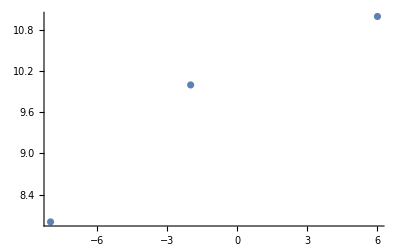

```mathematica
P1=ListPlot[data]
```

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[9.94595+0.209459 x]

```mathematica
model["BestFit"]
```

9.94595+0.209459 x

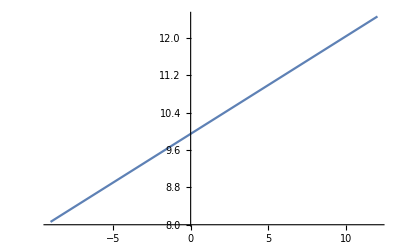

```mathematica
P2=Plot[9.945945945945946+0.20945945945945946 x,{x,-9,12}]
```

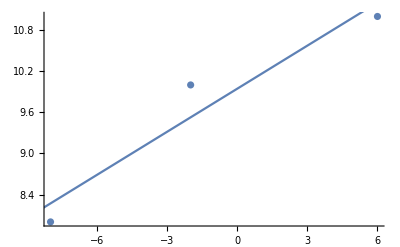

```mathematica
Show[P1,P2]
```

```mathematica
9.945945945945946+0.20945945945945946 x/.x->{-8,-2,6}
```

{8.27027,9.52703,11.2027}

```mathematica
{8.27027027027027,9.527027027027026,11.202702702702702}-{8,10,11}
```

{0.27027,-0.472973,0.202703}

```mathematica
1/(2π)Exp[-(y)^2] 1/(2π)/.y->{0.2702702702702702,-0.4729729729729737,0.20270270270270174}//N
```

{0.023546,0.0202529,0.0243106}

```mathematica
L0={0.02354598051605746,0.02025289432564488,0.0243106070806057};
```

```mathematica
evidence0=Product[L0[[i]],{i,1,3}]
```

0.0000115931

Ratio of evidences

```mathematica
evidence0/evidence1
```

4.23844×10^123

```mathematica
evidence0/evidence2
```

1.19097×10^14

```mathematica
evidence2/evidence1
```

3.55883×10^109